```mathematica
ClearAll["Global`*"]
```

```mathematica
fk[k1_,k2_,r_]:={1/(1/k1+1/k2),1/(1/(r*k1)+1/k2),1/(1/k1+1/(r*k2))}
frho[k1_,ρ_,r_]:=k1*{ρ/(1+ρ),(r*ρ)/(r+ρ),(r*ρ)/(1+r*ρ)}
K1=1;  (*The contour plot does not depend on the value of k1.*)
```

```mathematica
g[k_,r_]:={k/2,(r*k)/2,k/2}  (*Only works when R1 is retained in the reduced model (ρ>1)*)
```

```mathematica
Fitk[ρ_,r_]:=k/.Last[FindMinimum[Norm[(frho[k1,ρ,r]/.{k1->K1})-g[k,r]],{k,HarmonicMean[{k1,k1*ρ}]/.k1->K1}]]
RelErr[ρ_,log10r_]:=(Fitk[ρ,10^log10r]-HarmonicMean[{k1,k1*ρ}]/.k1->K1)/(HarmonicMean[{k1,k1*ρ}]/.k1->K1)
```

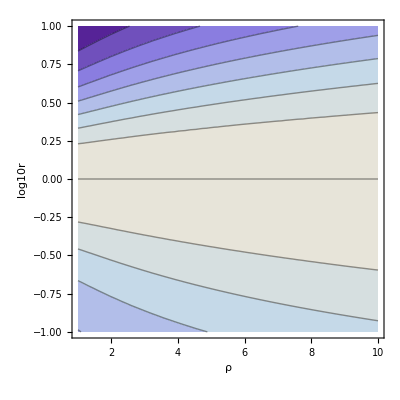

```mathematica
(*Needs["PlotLegends`"]*)
ContourPlot[RelErr[ρ,log10r],{ρ,1,10},{log10r,-1,1},AxesLabel->{"ρ","log10r"}]
```

```mathematica
jac=Simplify[Transpose[{D[fk[k1,k2,r],k1],D[fk[k1,k2,r],k2]}]]
```

{{k2^2/(k1+k2)^2,k1^2/(k1+k2)^2},{(k2^2 r)/(k2+k1 r)^2,(k1^2 r^2)/(k2+k1 r)^2},{(k2^2 r^2)/(k1+k2 r)^2,(k1^2 r)/(k1+k2 r)^2}}

```mathematica
{U,S,Vh}=SingularValueDecomposition[jac/.r->2];
```

```mathematica
S=FullSimplify[Vh,k1>0&&k2>0]/.k2->ρ k1
```

```mathematica
fklam[k1_,k2_,r_,λ_]:=λ*fk[k1,k2,r]+(1-λ)*{k1,k2,0};
```

```mathematica
Manipulate[ParametricPlot3D[fklam[k1,k2,r,λ]/.r->2,{k1,0.1,10},{k2,0.1,10}, AxesLabel->{"J1","J2","J3"},PlotRange->{{0,10},{0,10},{0,10}}],{λ,0,1}]
```